```mathematica
<<peeters`

peeters`setGitDir["../project/figures/phy487-qmsolids"]

fs=Style[#,FontSize->14]&;
```

peeters`

/Users/pjoot/project/figures/phy487-qmsolids

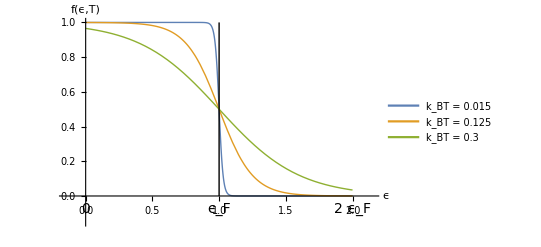

```mathematica
Clear[ tl ] ;
tl = Module[ {fd, tauLevels, eMax, space},
fd[ e_, mu_, tau_] = (E^((e - mu)/tau) + 1)^(-1) ;
eMax = 2 ;
space = 0.15 ;
tauLevels = {0.015, 0.125, 0.3} ;
Plot[ 
Evaluate@Table[fd[e, 1, tau], {tau, tauLevels}]
, {e, 0, eMax} 
, Ticks -> { None, Automatic}
, AxesLabel -> fs/@{ ϵ, f[ϵ, T]}
, PlotStyle-> Thick
, Epilog -> { Table[ Text[r Subscript[ϵ, F] // fs, {r, -space/2}], {r, 0, eMax}], Line[{{1, 0}, {1, 1}}]}
,PlotRange->{{-space,eMax+space},{-space,1}}
, PlotLegends-> Placed[ fs["k_BT = "  <> ToString[#]]   &/@tauLevels, {Right,Top} ]
]
]
```

```mathematica
peeters`exportForLatex["fermiDiracLevelCurvesFig1", tl]
```

{fermiDiracLevelCurvesFig1.eps,fermiDiracLevelCurvesFig1pn.png}

-Graphics-

```mathematica
Manipulate[
DynamicModule[ {fd, tauLevels,eMax},
fd[ e_, mu_, tau_] = (E^((e - mu)/tau) + 1)^(-1) ;
eMax = 2 (*mu*) ;
space = 0.15 ;
Plot[ 
fd[e, mu, tau]
, {e, 0, eMax} 
, PlotRange -> Full
, PlotStyle-> Thick
, AxesLabel -> { ϵ //fs, f[ϵ, T] //fs}
]
] 
, { {mu, 1, μ}, 0, 4, Appearance->"Open"}
, {{tau, 0.015,"k_BT" }, 0.001, 4, Appearance->"Open"}
]
```

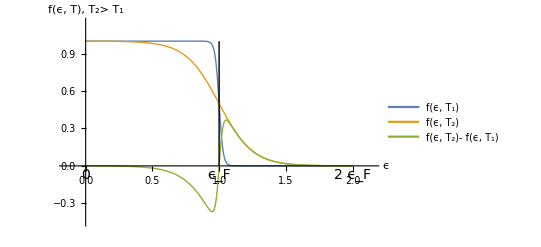

```mathematica
Clear[ t2 ] ;
t2 = Module[ {fd, tauLevels, eMax, a},
fd[ e_, mu_, tau_] = (E^((e - mu)/tau) + 1)^(-1) ;
tauLevels = {0.015, 0.125} ;
a = {fd[e, 1, #] &/@ tauLevels, fd[ e, 1, tauLevels[[2]]]- fd[ e, 1, tauLevels[[1]]]} // Flatten ;
eMax = 2 ;
space = 0.15 ;

Plot[ 
Evaluate@a
, {e, 0, eMax} 
, Ticks -> { None, Automatic}
, AxesLabel -> fs/@{ ϵ , "f(ϵ, T), T_2> T_1" }
, Epilog -> { 
Table[ Text[(r Subscript[ϵ, F]) //fs, {r, -space/2}], {r, 0, eMax}],
Line[{{1, 0}, {1, 1}}](*,
Text["μ = E_F", {1, 1}]*)
}
, PlotRange->{{-space,eMax+space},{-3space,1 + space}}
, PlotStyle-> Thick
, PlotLegends-> Placed[
fs/@ {
"f(ϵ, T_1)" , "f(ϵ, T_2)" , "f(ϵ, T_2)- f(ϵ, T_1)" 
}, {Right,Top} ]
]
]
```

```mathematica
peeters`exportForLatex["fermiDiracLevelCurvesFig2", t2]
```

{fermiDiracLevelCurvesFig2.eps,fermiDiracLevelCurvesFig2pn.png}

-Graphics-

```mathematica
Clear[ t3 ] ;
t3 = Module[ {fd, dfd, tauLevels, eMax, a},
fd[ e_, mu_, tau_] = (E^((e - mu)/tau) + 1)^(-1) ;
dfd[ e_, mu_, tau_ ] = D[ fd[e, mu, tau], tau] ;
tauLevels = {0.01, 0.02, 0.03}*3 ;
a = {fd[e, 1, #] &/@ tauLevels, dfd[e, 1, #] &/@ tauLevels} // Flatten ;
eMax = 2 ;
space = 0.15 ;

Plot[ 
Evaluate@a
, {e, 0, eMax} 
, Ticks -> { None, Automatic}
, AxesLabel -> fs/@{ ϵ , "T_3> T_2> T_1"}
, Epilog -> { 
Table[ Text[(r Subscript[ϵ, F]) //fs, {r, -6 space}], {r, 0, eMax}],
Line[{{1, 0}, {1, 1}}]
}
, PlotRange -> { Full, {-8, 8}}
, PlotStyle-> Thick
, PlotLegends->  Placed[
 {
"f(ϵ, T_1)", 
"f(ϵ, T_2)", 
"f(ϵ, T_3)",
 "∂f(ϵ, T)/∂T |_(T = SubscriptBox[T, 1])", 
"∂f(ϵ, T)/∂T |_(T = SubscriptBox[T, 2])",
 "∂f(ϵ, T)/∂T |_(T = SubscriptBox[T, 3])"
}, {Right, Right}]
]
]
```

-Graphics-

{fermiDiracLevelCurvesAndDerivativesFig3.eps,fermiDiracLevelCurvesAndDerivativesFig3pn.png}

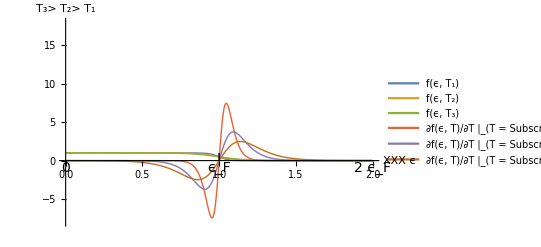

```mathematica
peeters`exportForLatex["fermiDiracLevelCurvesAndDerivativesFig3", t3]
```

```mathematica
Clear[ t4 ] ;
t4 = Module[ {fd, dfd, tauLevels, eMax, a},
fd[ e_, mu_, tau_] = (E^((e - mu)/tau) + 1)^(-1) ;
dfd[ e_, mu_, tau_ ] = D[ fd[e, mu, tau], e] ;
tauLevels = {0.01, 0.02, 0.03}*3 ;
a = {fd[e, 1, #] &/@ tauLevels, dfd[e, 1, #] &/@ tauLevels} // Flatten ;
eMax = 2 ;
space = 0.15 ;

Plot[ 
Evaluate@a
, {e, 0, eMax} 
, Ticks -> { None, Automatic}
, AxesLabel -> fs/@{ ϵ, "T_3> T_2> T_1" }
, Epilog -> { 
Table[ Text[(r Subscript[ϵ, F]) //fs, {r, -4 space}], {r, 0, eMax}],
Line[{{1, 0}, {1, 1}}]
}
, PlotRange -> Full
, PlotLegends->  Placed[
{
"f(ϵ, T_1)", "f(ϵ, T_2)", "f(ϵ, T_3)", "∂f(ϵ, T)/∂ϵ |_(T = SubscriptBox[T, 1])", "∂f(ϵ, T)/∂ϵ |_(T = SubscriptBox[T, 2])", "∂f(ϵ, T)/∂ϵ |_(T = SubscriptBox[T, 3])"
}, {Right,Right} ]
]
]
```

-Graphics-

{fermiDiracLevelCurvesAndEnergyDerivativesFig4.eps,fermiDiracLevelCurvesAndEnergyDerivativesFig4pn.png}

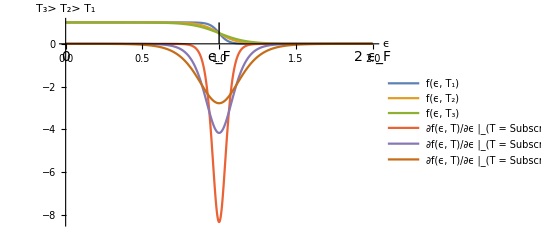

```mathematica
peeters`exportForLatex["fermiDiracLevelCurvesAndEnergyDerivativesFig4", t4]
```

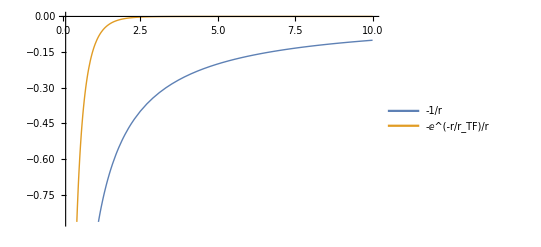

{thomasFermiScreeningFig5.eps,thomasFermiScreeningFig5pn.png}

```mathematica
Clear[t5]
t5 = Module[{a, f},
f[r_, rtf_] = -E^(- r/rtf)/r ;
a = f[r, #] &/@ {Infinity, 1/2 } ;

Plot[   Evaluate@a, {r, 0.1, 10}
, Ticks -> None
, PlotStyle-> Thick
, PlotLegends->  Placed[ fs[f[r, #]] &/@ {Infinity, Subscript[r, TF] }, {Right,Bottom} ]
]
]

(*peeters`exportForLatex["thomasFermiScreeningFig5", t5]*)
```